```mathematica
Clear[zeta,zetb,zetc]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
zeta[n_,s_,z_,k_]:=zeta[n,s,z,k]=1+((z+1)/k-1)Sum[j^-s zeta[Floor[n/j],s,z,k+1],{j,2,n}]
zetb[n_,s_,z_,k_]:=zetb[n,s,z,k]=1+((z)/k)Sum[j^-s zetb[Floor[n/j],s,z,k+1],{j,2,n}]
zetc[n_,s_,z_,k_]:=zetc[n,s,z,k]=1+((z-1)/k+1)Sum[j^-s zetc[Floor[n/j],s,z,k+1],{j,2,n}]
zetam1[n_,s_,0]:=UnitStep[n-1]
zetam1[n_,s_,k_]:=Sum[j^-s zetam1[n/j,s,k-1],{j,2,n}]
altlogzeta[n_,s_]:=Sum[k^-1 zetam1[n,s,k],{k,1,Log[2,n]}]
altd[n_, s_,z_] := Sum[ (-1)^(k)bin[z,k]zetam1[n,s,k],{k,0,Log[2,n]}]
maind[n_, s_,z_] := Sum[ bin[z,k]zetam1[n,s,k],{k,0,Log[2,n]}]
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_,z_]:=Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[n]}]
altdz[n_,z_]:=Product[ Binomial[z,p[[2]]],{p,FI[n]}]


Expand[zeta[100,0,z,1]]

Expand[altd[100,0,z]]
```

1+(428 z)/15+(16289 z^2)/360+(331 z^3)/16+(611 z^4)/144+(67 z^5)/240+(7 z^6)/720

1-(6088 z)/15+(148229 z^2)/360-(1873 z^3)/16+(1835 z^4)/144-(137 z^5)/240+(7 z^6)/720

```mathematica
Expand[zetc[100,0,z,1]]
```

1+(6088 z)/15+(148229 z^2)/360+(1873 z^3)/16+(1835 z^4)/144+(137 z^5)/240+(7 z^6)/720

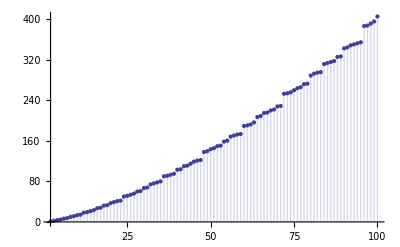

```mathematica
DiscretePlot[ D[Expand[zetc[n,0,z,1]],z]/.z->0,{n,2,100}]
```

```mathematica
Table[{n,D[altd[n,0,z]-altd[n-1,0,z],z]/.z->0,D[ maind[n,0,z]-maind[n-1,0,z],z]/.z->0},{n,2,30}]//TableForm
```

2 | -1 | 1
3 | -1 | 1
4 | -3/2 | 1/2
5 | -1 | 1
6 | -2 | 0
7 | -1 | 1
8 | -7/3 | 1/3
9 | -3/2 | 1/2
10 | -2 | 0
11 | -1 | 1
12 | -4 | 0
13 | -1 | 1
14 | -2 | 0
15 | -2 | 0
16 | -15/4 | 1/4
17 | -1 | 1
18 | -4 | 0
19 | -1 | 1
20 | -4 | 0
21 | -2 | 0
22 | -2 | 0
23 | -1 | 1
24 | -8 | 0
25 | -3/2 | 1/2
26 | -2 | 0
27 | -7/3 | 1/3
28 | -4 | 0
29 | -1 | 1
30 | -6 | 0

```mathematica
(-1)^(1) bin[-z,1](-1)^(1) bin[-z,1](-1)^(1) bin[-z,1]
```

z^3

```mathematica
FullSimplify[z+3 (-1+z) z+(-2+z) (-1+z) z]
```

z^3

```mathematica
Expand[-z+3 (-1+z) z-(-2+z) (-1+z) z]
```

-6 z+6 z^2-z^3

```mathematica
Expand[-z+(-1+z) z]
```

-2 z+z^2

```mathematica
altd[4,0,z]-altd[3,0,z]
```

-z+1/2 (-1+z) z

```mathematica
altd[30,0,z]-altd[29 - 1,0,z]
```

-2 z+3 (-1+z) z-(-2+z) (-1+z) z

```mathematica
tt[k_]:=Sum[ (-1)^(j)bin[k-1,j-1]bin[ z,j],{j,1,k}]
```

```mathematica
Expand[tt[5] tt[2]]
```

(93 z^2)/10-(559 z^3)/40+(113 z^4)/16-(73 z^5)/48+(11 z^6)/80-z^7/240

```mathematica
Sum[ (-1)^(j)bin[3-1,j-1]bin[ z,j],{j,1,3}]
```

-z+(-1+z) z-1/6 (-2+z) (-1+z) z

```mathematica
Expand[zeta[10,0,z,1]]
```

1+(16 z)/3+(7 z^2)/2+z^3/6

```mathematica
Expand[zeta[10000,0,z,1]]
```

1+(56175529 z)/45045+(5304616687 z^2)/1663200+(64238883431 z^3)/19958400+(3688608229 z^4)/2177280+(11603252491 z^5)/21772800+(4483862353 z^6)/43545600+(557009347 z^7)/43545600+(2872319 z^8)/2903040+(688397 z^9)/14515200+(58651 z^10)/43545600+(8339 z^11)/479001600+(17 z^12)/95800320+z^13/6227020800

```mathematica
Expand[zeta[500,-1,z,1]]
```

1+(1878019 z)/84+(120118007 z^2)/2520+(6961123 z^3)/180+(1657477 z^4)/120+(45367 z^5)/18+(3131 z^6)/15+(3571 z^7)/315+(26 z^8)/315

```mathematica
Expand[zeta[50,1,z,1]]
```

1+(36227089580823978984163 z)/18594267025475980238400+(2722987611283 z^2)/2248776129600+(1770229 z^3)/5702400+(41 z^4)/1440+(13 z^5)/11520

```mathematica
Expand[zeta[20,N[ZetaZero[1]],z,1]]
```

1-(2.06564-0.208919 ⅈ) z+(1.0225-0.278071 ⅈ) z^2-(0.268006-0.181271 ⅈ) z^3+(0.000833781-0.0103832 ⅈ) z^4

```mathematica
N[Expand[D[zeta[80,s,z,1],s]]/.s->0]
```

-79.4645 z-120.818 z^2-62.7616 z^3-9.80744 z^4-0.815798 z^5-0.00577623 z^6

```mathematica
N[ZetaZero[1]]
```

0.5+14.1347 ⅈ

```mathematica
Clear[K,zeta,zetb]
K[n_] := K[n] = FullSimplify[ MangoldtLambda[n]/Log[n]]
zeta[n_,s_,z_,k_]:=zeta[n,s,z,k]=Expand[1+((z+1)/k-1)Sum[j^-s zeta[Floor[n/j],s,z,k+1],{j,2,n}]]
zetb[n_,s_,z_,k_]:=zetb[n,s,z,k]=Expand[1+z/k Sum[If[ K[j]==0,0,K[j]j^-s zetb[Floor[n/j],s,z,k+1]],{j,2,n}]]
```

```mathematica
Timing[zeta[100000,0,z,1]]
```

{7.051,1+(991892879 z)/102960+(16611877533197 z^2)/605404800+(27613425421567 z^3)/864864000+(8883298064606291 z^4)/435891456000+(82938597121 z^5)/10264320+(12123475378339 z^6)/5748019200+(987114594581 z^7)/2612736000+(6832898553167 z^8)/146313216000+(53237749 z^9)/13063680+(1772592397 z^10)/7315660800+(20466961 z^11)/2052864000+(30323737 z^12)/114960384000+(841 z^13)/186810624+(9773 z^14)/209227898880+(71 z^15)/373621248000+(17 z^16)/20922789888000}

```mathematica
Timing[zetb[100000,0,z,1]]
```

{7.473,1+(991892879 z)/102960+(16611877533197 z^2)/605404800+(27613425421567 z^3)/864864000+(8883298064606291 z^4)/435891456000+(82938597121 z^5)/10264320+(12123475378339 z^6)/5748019200+(987114594581 z^7)/2612736000+(6832898553167 z^8)/146313216000+(53237749 z^9)/13063680+(1772592397 z^10)/7315660800+(20466961 z^11)/2052864000+(30323737 z^12)/114960384000+(841 z^13)/186810624+(9773 z^14)/209227898880+(71 z^15)/373621248000+(17 z^16)/20922789888000}

```mathematica
D[z^3/6,z]
```

z^2/2

```mathematica
D[z,z]
```

1

```mathematica
D[x^z,z]
```

x^z Log[x]

```mathematica
D[x^z,{z,2}]
```

x^z Log[x]^2

```mathematica
D[x^z,{z,3}]
```

x^z Log[x]^3

```mathematica
bin[z_,k_]:=bin[z,k]=Product[z-j,{j,0,k-1}]/k!
E2a[n_,k_, a_,s_]:= E2a[n,k,a,s]=Sum[ j^(-s)E2a[n/j,k-1,a,s],{j,2,n}]-a Sum[ (j a)^(-s)E2a[n/(a j),k-1,a,s],{j,1,n/a}];E2a[n_,0,a_,s_]:=UnitStep[n-1]
E1b[n_,z_,b_,s_]:=Sum[ bin[z,k] E2a[n,k,b,s],{k,0,If[ b < 2, Log[b,n],Log[2,n]]}]
```

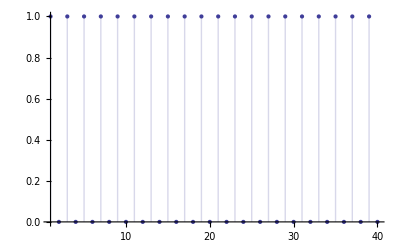

```mathematica
DiscretePlot[ E1b[n,1,2,0],{n,1,40}]
```

```mathematica
Limit[(1-5^(1-s))Zeta[s],s->2]
```

(2 π^2)/15

```mathematica
N[2 Pi^2/15]
```

1.31595

```mathematica
N[Sum[ (Mod[n,5]-Mod[n-1,5])/n^2,{n,1,40}]]
```

1.31476

```mathematica
Expand[E1b[100,z,5,0]]
```

1+(331 z)/30-(7711 z^2)/360+(403 z^3)/48+(131 z^4)/144+(17 z^5)/240+(7 z^6)/720

```mathematica
zeros[n_,s_]:=List@@NRoots[Expand[E1b[n,z,10,s]]==0,z][[All,2]]
```

```mathematica
zeros[105,N[ZetaZero[1]]]
```

{-18.223-4.89962 ⅈ,-0.447427+0.51221 ⅈ,0.259219+21.386 ⅈ,0.828298-0.480269 ⅈ,1.11297+3.10139 ⅈ,1.14551+0.121388 ⅈ}

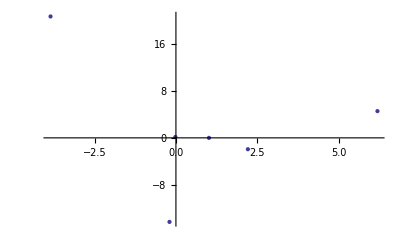

```mathematica
ListPlot[Table[{Re[n],Im[n]},{n,zeros[104,N[ZetaZero[1]]]}]]
```

```mathematica
t[n_,x_, y_]:=y (Floor[n/y]-Floor[(n-1)/y])-x (Floor[n/x]-Floor[(n-1)/x])
Dd[n_,s_,z_,y_,x_,k_]:=Expand[1+y^(s-1)((z+1)/k-1)Sum[t[n,x,y]j^-s Dd[n/j,s,z,y,x,k+1],{j,y+1,n y}]]
```

```mathematica
Dd[100,0,1,2,1,1]
```

100

```mathematica
t[7,1,2]
```

-1

```mathematica
Zeta[6]
```

π^6/945

```mathematica
n^p + Sum[ BernoulliB[k] p! n^(p-k+1)/(k! (p-k+1)!),{k,0,p}]/.p->4
```

-n/30+n^3/3+n^4/2+n^5/5

```mathematica
Expand[Sum[ j^(3/2),{j,1,n}]]
```

HarmonicNumber[n,-3/2]

```mathematica
Expand[zeta[12,0,z,1]]
```

1+(19 z)/3+4 z^2+(2 z^3)/3

```mathematica
zerosx[n_,s_]:=List@@ NRoots[Expand[zeta[n,s,z,1]]==0,z][[All,2]]
```

```mathematica
N[zerosx[100,0]]
```

{-0.933809,-0.0372047,-11.1997-12.3982 ⅈ,-11.1997+12.3982 ⅈ,-2.67195-1.86184 ⅈ,-2.67195+1.86184 ⅈ}

```mathematica
N[zerosx[10000,0]]
```

{-1005.17,-25.9197-61.2147 ⅈ,-25.9197+61.2147 ⅈ,-12.5619,-9.95084-13.237 ⅈ,-9.95084+13.237 ⅈ,-4.34989-4.84639 ⅈ,-4.34989+4.84639 ⅈ,-2.23696-1.84432 ⅈ,-2.23696+1.84432 ⅈ,-1.17804-0.181571 ⅈ,-1.17804+0.181571 ⅈ,-0.000803511}

```mathematica
Product[1+1/j,{j,zerosx[12,0]}]
```

-2.

```mathematica
19./3
```

6.33333

```mathematica
FI[n_]:=FactorInteger[n];FI[1]:={}
fz2[n_,z_]:=Product[If[p[[1]]==2,-z Hypergeometric2F1[1-p[[2]],1-z,2,-1],(-1)^p[[2]] Binomial[-z,p[[2]]]],{p,FI[n]}]
fz3[n_,z_]:=Product[If[p[[1]]==2,Sum[  (-1)^(k)Binomial[p[[2]]-1,k-1]Binomial[z,k],{k,1,p[[2]]}],(-1)^p[[2]] Binomial[-z,p[[2]]]],{p,FI[n]}]
ff[n_, k_] := Sum[ (-1)^(j+1)ff[Floor[n/j],k-1],{j,2,n}]
ff[n_, 0] := UnitStep[n-1]
fz[n_, z_] := Sum[ bin[ z,k] ff[n,k],{k,0,Log[2,n]}]
```

```mathematica
Table[ {n,FullSimplify[fz2[n,z]-(fz[n,z]-fz[n-1,z])]},{n,2,20}]//TableForm
```

2 | 0
3 | 0
4 | 0
5 | 0
6 | 0
7 | 0
8 | 0
9 | 0
10 | 0
11 | 0
12 | 0
13 | 0
14 | 0
15 | 0
16 | 0
17 | 0
18 | 0
19 | 0
20 | 0

```mathematica
Sum[  (-1)^(k)Binomial[p-1,k-1]Binomial[z,k],{k,1,p}]
```

-z Hypergeometric2F1[1-p,1-z,2,-1]

```mathematica
Expand[(-1)^(k)Binomial[p-1,k-1]Binomial[z,k]]
```

(-1)^k Binomial[-1+p,-1+k] Binomial[z,k]

```mathematica
Expand[Sum[  (-1)^k bin[p-1,k-1]bin[z,k],{k,1,p}]/.p->4]
```

-(15 z)/4+(83 z^2)/24-(3 z^3)/4+z^4/24

```mathematica
Expand[fz[16,z]-fz[15,z]]
```

-(15 z)/4+(83 z^2)/24-(3 z^3)/4+z^4/24

```mathematica
Expand[-z Hypergeometric2F1[1-p,1-z,2,-1]/.p->0]
```

1-2^z

```mathematica
fz2a[n_,z_]:=Product[If[p[[1]]==2,-z Hypergeometric2F1[1-p[[2]],1-z,2,-1],(-1)^p[[2]] Binomial[-z,p[[2]]]],{p,FI[n]}]
fz3a[n_,z_]:=Product[If[p[[1]]==2,Sum[  (-1)^k Binomial[p[[2]]-1,k-1]Binomial[z,k],{k,1,p[[2]]}],Binomial[z+p[[2]]-1,p[[2]]]],{p,FI[n]}]
fz3x[n_,z_]:=Product[Sum[  If[ p[[1]]==2,(-1)^k,1] Binomial[p[[2]]-1,k-1]Binomial[z,k],{k,1,p[[2]]}],{p,FI[n]}]
fz3y[n_,z_]:=Product[Sum[  (-1)^(k(Floor[p[[1]]/2]-Floor[(p[[1]]-1)/2])) Binomial[p[[2]]-1,k-1]Binomial[z,k],{k,1,p[[2]]}],{p,FI[n]}]
fz4a[p_,z_]:=Table[  (-1)^k Binomial[p-1,k-1]Binomial[z,k],{k,1,p}]
fz4b[p_,z_]:=Binomial[z+p-1,p]
Table[D[fz3y[n,z],z]/.z->0,{n,1,20}]//TableForm
```

0
-1
1
-3/2
1
0
1
-7/3
1/2
0
1
0
1
0
0
-15/4
1
0
1
0

```mathematica
fz4a[3,4]
```

{-4,12,-4}

```mathematica
fz4b[3,4]
```

20

```mathematica
Sum[   Binomial[p-1,k-1]Binomial[z,k],{k,1,p}]/.p->3
```

Gamma[3+z]/(6 Gamma[z])

```mathematica
Sum[(-1)^k   Binomial[p-1,k-1]Binomial[z,k],{k,1,p}]/.p->3
```

-1/6 z (14-9 z+z^2)

```mathematica
f[a_] := Floor[a/2]-Floor[(a-1)/2]
```

```mathematica
Table[f[n],{n,1,20}]
```

{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1}

```mathematica
bin[z_,k_]:=bin[z,k]=Product[z-j,{j,0,k-1}]/k!
E2a[n_,k_, a_,s_]:= E2a[n,k,a,s]=Sum[ j^(-s)E2a[n/j,k-1,a,s],{j,2,n}]-a Sum[ (j a)^(-s)E2a[n/(a j),k-1,a,s],{j,1,n/a}];E2a[n_,0,a_,s_]:=UnitStep[n-1]
E1b[n_,z_,b_,s_]:=Sum[ bin[z,k] E2a[n,k,b,s],{k,0,If[ b < 2, Log[b,n],Log[2,n]]}]
fzr[n_,s_,z_]:=n^-s Product[If[p[[1]]==2,-z Hypergeometric2F1[1-p[[2]],1-z,2,-1],(-1)^p[[2]]bin[-z,p[[2]]]],{p,FI[n]}]
Expand[Sum[ fzr[n,-1,z],{n,1,100}]]
```

1+(10301 z)/60-(235459 z^2)/360+(2363 z^3)/4-(12797 z^4)/72+(286 z^5)/15-(32 z^6)/45

```mathematica
Expand[E1b[100,z,2,-1]]
```

1+(10301 z)/60-(235459 z^2)/360+(2363 z^3)/4-(12797 z^4)/72+(286 z^5)/15-(32 z^6)/45

```mathematica
Timing[Expand[Sum[ fzr[n,N[ZetaZero[1]],z],{n,1,10000000}]]]
```

{2373.77,(1.+0. ⅈ)-(45.4558+48.4997 ⅈ) z+(140.588+164.395 ⅈ) z^2-(191.246+238.877 ⅈ) z^3+(152.097+199.937 ⅈ) z^4-(80.3319+108.801 ⅈ) z^5+(30.3631+41.1341 ⅈ) z^6-(8.62493+11.2783 ⅈ) z^7+(1.90012+2.31031 ⅈ) z^8-(0.329937+0.359479 ⅈ) z^9+(0.0452778+0.0424413 ⅈ) z^10-(0.00487763+0.00370671 ⅈ) z^11+(0.00040802+0.000228966 ⅈ) z^12-(0.0000261843+9.41988×10^-6 ⅈ) z^13+(1.26949×10^-6+2.18011×10^-7 ⅈ) z^14-(4.554×10^-8-3.03041×10^-12 ⅈ) z^15+(1.18086×10^-9-1.83197×10^-10 ⅈ) z^16-(2.16758×10^-11-6.08217×10^-12 ⅈ) z^17+(2.75011×10^-13-9.65399×10^-14 ⅈ) z^18-(2.34225×10^-15-8.61328×10^-16 ⅈ) z^19+(1.25981×10^-17-4.23332×10^-18 ⅈ) z^20-(3.5056×10^-20-1.60456×10^-20 ⅈ) z^21+(5.09704×10^-23-3.36529×10^-23 ⅈ) z^22-(8.77986×10^-27+1.0064×10^-26 ⅈ) z^23}